```mathematica
FT=∑_(i=0)^18 F[i];

FTT=∑_(i=0)^3 F[i];
```

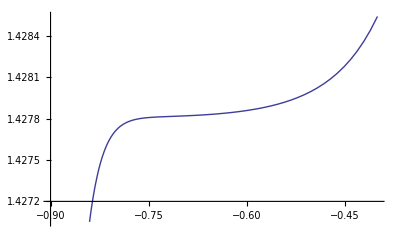

1.42782

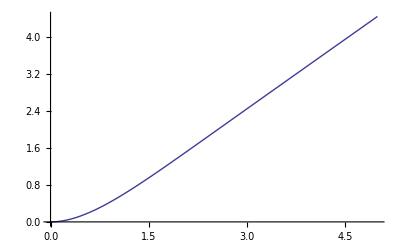

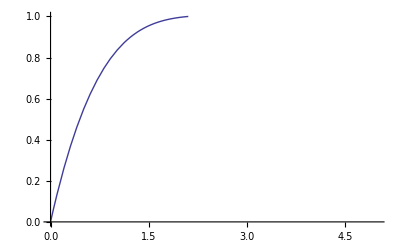

```mathematica
Fh=D[FT,{η,2}]/.{η->0,M->0.5,Δ->1};
fff=FT/.{h->-.7,M->0.5,Δ->1};
ffft=FTT/.{h->-.7,M->0.5,Δ->1};
Plot[Fh,{h,-.9,-0.4}]
N[D[fff,{η,2}]/.η->0]
pf=Plot[fff,{η,0,5}]
pfd=D[fff,η];
pfp=Plot[pfd,{η,0,5},PlotRange->{0,1}]
```

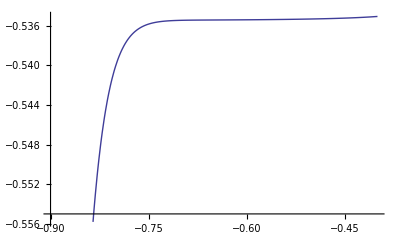

-0.535455

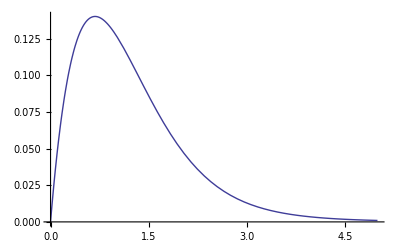

```mathematica
GT=∑_(i=0)^15 G[i];
Gh=D[GT,η]/.{η->0,M->0.5,Δ->1};
ggg=GT/.{h->-.7,M->0.5,Δ->1};
Plot[Gh,{h,-.9,-.4}]
N[D[ggg,η]/.η->0]
pg=Plot[-ggg,{η,0,5}]
```

```mathematica
HT=∑_(i=0)^16 H[i];
```

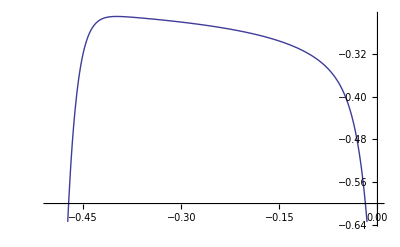

-0.260114

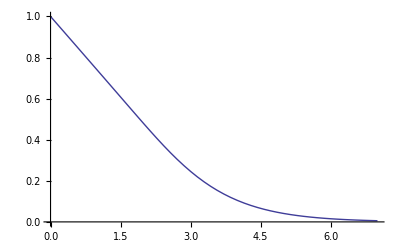

```mathematica
Hh=D[HT,η]/.{η->0,M->0.5,Δ->1,R->.1};
hhh=HT/.{h->-.3,M->0.5,Δ->1,R->.1};
Plot[Hh,{h,-.5,0}]
N[D[hhh,η]/.η->0]
ph=Plot[hhh,{η,0,7}]
```

```mathematica
eq1:=D[f[η],{η,3}]+f[η]*D[f[η],{η,2}]+Δ D[h[η],η]+1/M(1-D[f[η],η])+P(1-D[f[η],η]^2)/.{M->0.5,Δ->0.8,P->0.1}
eq2:=g D[h[η],{η,2}]-2(2h[η]+D[f[η],{η,2}])/.g->2
eq3:=(3R+4)D[Θ[η],{η,2}]+3R Pr f[η]*D[Θ[η],η]/.{Pr->0.7,R->1}
an=NDSolve[{eq1==0,eq2==0,eq3==0,f[0]==0,f'[0]==0,f'[2.49]==1,h[0]==0,h[2.49]==0,Θ[0]==1,Θ[2.49]==0},{f[η],f''[η],h'[η],h[η],Θ[η],Θ'[η]},{η,0,3}]
Evaluate[f''[η]/.an]/.η->0
Evaluate[h'[η]/.an]/.η->0
Evaluate[Θ'[η]/.an]/.η->0
```

{{f[η]→InterpolatingFunction[{{0.,3.}},<>][η],f''[η]→InterpolatingFunction[{{0.,3.}},<>][η],h'[η]→InterpolatingFunction[{{0.,3.}},<>][η],h[η]→InterpolatingFunction[{{0.,3.}},<>][η],Θ[η]→InterpolatingFunction[{{0.,3.}},<>][η],Θ'[η]→InterpolatingFunction[{{0.,3.}},<>][η]}}

{1.44868}

{-0.53403}

{-0.467737}

```mathematica
eq1:=D[f[η],{η,3}]+f[η]*D[f[η],{η,2}]+Δ D[h[η],η]+1/M(1-D[f[η],η])+P(1-D[f[η],η]^2)/.{M->0.5,Δ->.8,P->0.1}
eq2:=g D[h[η],{η,2}]-2(2h[η]+D[f[η],{η,2}])/.g->2
eq3:=(3R+4)D[Θ[η],{η,2}]+3R Pr f[η]*D[Θ[η],η]/.{Pr->0.7,R->1}
an=NDSolve[{eq1==0,eq2==0,eq3==0,f[0]==0,f'[0]==0,f'[6]==1,h[0]==0,h[6]==0,Θ[0]==1,Θ[6]==0},{f[η],f'[η],f''[η],h[η],h'[η],Θ[η],Θ'[η]},η,Method->{"Shooting","StartingInitialConditions"->{f[0]==0,f'[0]==0,f''[0]==1.4855244071208615,h[0]==0,h'[0]==-0.5336439213976489,Θ[0]==1,Θ'[0]==-0.46769928639515984}}]
Evaluate[f''[η]/.an]/.η->0
Evaluate[h'[η]/.an]/.η->0
Evaluate[Θ'[η]/.an]/.η->0
```

{{f[η]→InterpolatingFunction[{{0.,6.}},<>][η],f'[η]→InterpolatingFunction[{{0.,6.}},<>][η],f''[η]→InterpolatingFunction[{{0.,6.}},<>][η],h[η]→InterpolatingFunction[{{0.,6.}},<>][η],h'[η]→InterpolatingFunction[{{0.,6.}},<>][η],Θ[η]→InterpolatingFunction[{{0.,6.}},<>][η],Θ'[η]→InterpolatingFunction[{{0.,6.}},<>][η]}}

{1.44686}

{-0.53543}

{-0.360133}

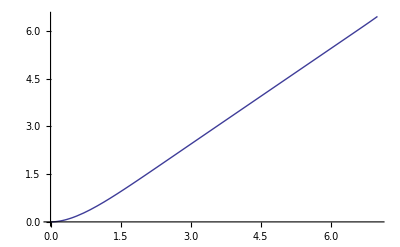

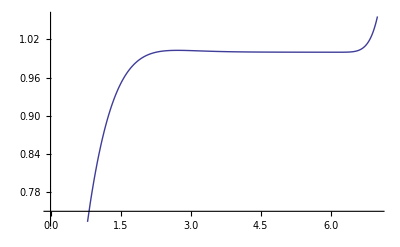

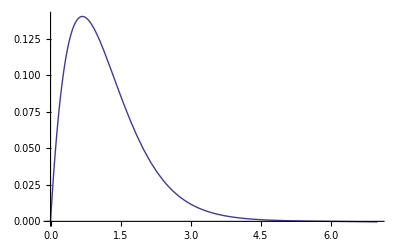

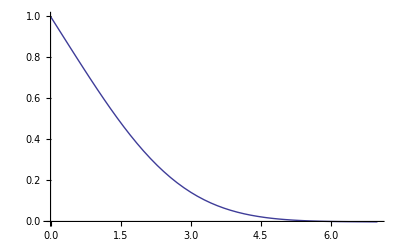

```mathematica
ffff=Evaluate[f[η]/.an];
ffffp=Evaluate[f'[η]/.an];
hhhh=-Evaluate[h[η]/.an];
ΘΘΘΘ=Evaluate[Θ[η]/.an];
pfn=Plot[ffff,{η,0,7}]
pfnp=Plot[ffffp,{η,0,7}]
phn=Plot[hhhh,{η,0,7}]
pΘn=Plot[ΘΘΘΘ,{η,0,7}]
```

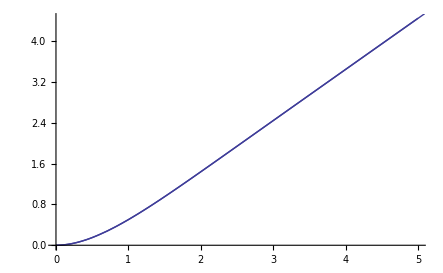

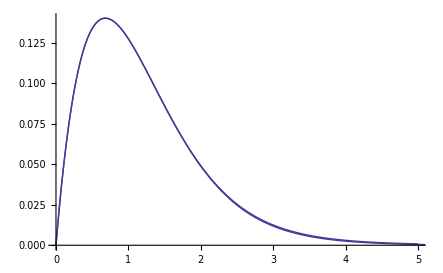

```mathematica
Show[pf,pfn]
Show[pg,phn]
```

```mathematica
fn=Evaluate[f[η]/.an][[1]];
fnp=Evaluate[f'[η]/.an][[1]];
gn=Evaluate[h[η]/.an][[1]];
outf=Table[{η,fff,fn},{η,0,6,0.005}];
outfp=Table[{η,pfd,fnp},{η,0,6,0.005}];
outg=Table[{η,-ggg,-gn},{η,0,6,0.005}];
hcurve=Table[{h,Fh,Gh},{h,-2,0,0.005}];
Export["D:\\Project\\Complete\\Article\\Analytic Approximate Solutions for Heat Transfer of a Micropolar Fluid through a Porous Medium with Radiation\\Data\\M=0.5\\fd.8.dat",outf];
Export["D:\\Project\\Complete\\Article\\Analytic Approximate Solutions for Heat Transfer of a Micropolar Fluid through a Porous Medium with Radiation\\Data\\M=0.5\\fpd.8.dat",outfp];
Export["D:\\Project\\Complete\\Article\\Analytic Approximate Solutions for Heat Transfer of a Micropolar Fluid through a Porous Medium with Radiation\\Data\\M=0.5\\gd.8.dat",outg];

Export["D:\\Project\\Complete\\Article\\Analytic Approximate Solutions for Heat Transfer of a Micropolar Fluid through a Porous Medium with Radiation\\Data\\M=0.5\\h.8.dat",hcurve];
```

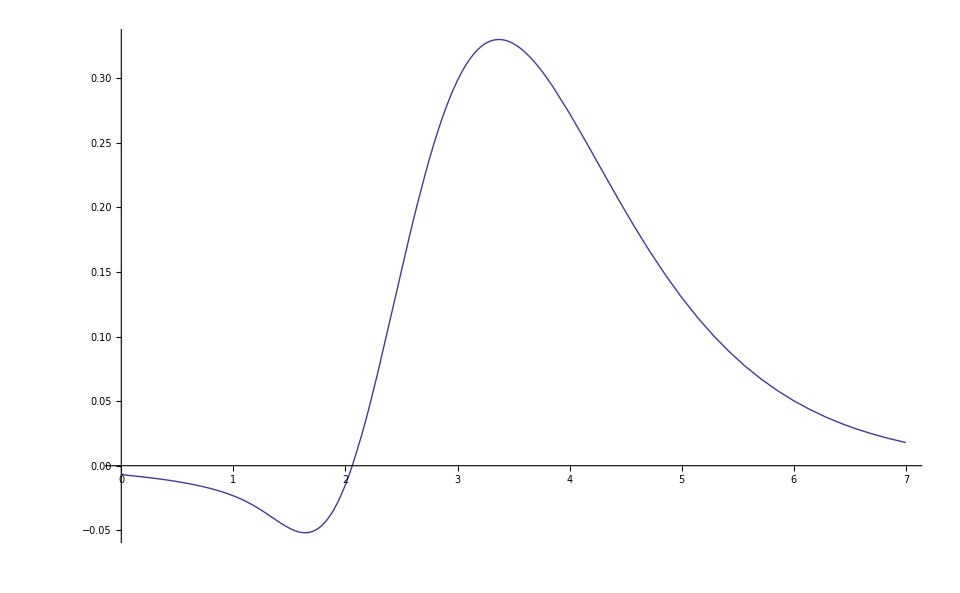

```mathematica
fff=FT/.{h->-.7,M->0.5,Δ->1};
hhh=HT/.{h->-.35,M->0.5,Δ->1,R->.1};
P=0.1;
g=2;
kkk=(3R+4)D[hhh,{η,2}]+3*R*Pr*fff*D[hhh,η]/.{M->0.5,Δ->1,Pr->0.7,R->.1};
Plot[kkk,{η,0,7}]
```

```mathematica
Errort=Table[{η,kkk*0.0001},{η,0,9,0.005}];
Export["D:\\Project\\Complete\\Article\\Analytic Approximate Solutions for Heat Transfer of a Micropolar Fluid through a Porous Medium with Radiation\\Data\\Error\\Errort-.4.dat",Errort];
```

```mathematica
hhh=HT/.{h->-.2,M->0.5,Δ->.8};
fff=FT/.{h->-.7,M->0.5,Δ->.8};
P=0.1;
g=2;
jjj=D[fff,{η,3}]+fff*D[fff,{η,2}]+Δ*D[ggg,η]+(1/M)*(1-D[fff,η])+P*(1-D[fff,η]^2)/.{M->0.5,Δ->.8};
Plot[jjj,{η,0,7}]
```